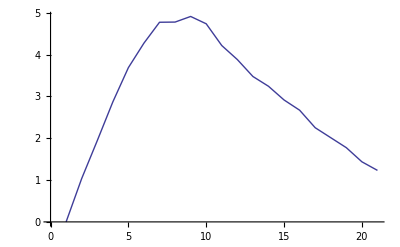
6.4364
-Graphics-

```mathematica
Remove@mcplot;

mcplot[y_,cosmin_,acgoal_,prgoal_,partlist_List,Xmax_: 10,points_: 50,method_]:=
Block[{dX=(Xmax-2)/points,cos,solx1p,int},

solx1p=-((cos (-2+X^2) x2+Sqrt[(1+x2^2) (-4 X^2+X^4+4 (-1+cos^2) x2^2)])/(-2+2 (-1+cos^2) x2^2));
cos=cos1 cos2+√(1-cos1^2) √(1-cos2^2) Cos[2 p1 π] Cos[2 p2 π]+√(1-cos1^2) √(1-cos2^2) Sin[2 p1 π] Sin[2 p2 π];

int=Evaluate[
Boole[cos1 cos2+√(1-cos1^2) √(1-cos2^2) Cos[2 p1 π] Cos[2 p2 π]+√(1-cos1^2) √(1-cos2^2) Sin[2 p1 π] Sin[2 p2 π]>cosmin]* 
Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0] *
1/(2 (-cos x2+(solx1p √(1+x2^2))/(√(1+solx1p^2)))) *
solx1p^3/Sqrt[solx1p^2+1] 1/(Exp[1/(11.24/(2 π) y) Sqrt[1+solx1p^2]]+1) x2^3/Sqrt[x2^2+1] 1/(Exp[1/(11.24/(2 π) y) Sqrt[1+x2^2]]+1)];

TableForm@Timing@ListPlot[
Table[
X NIntegrate[int,{x2,0,Sqrt[X^2 (X^2-1)/4]},{cos1,0,1},{cos2,0,1},{p1,0,1},{p2,0,1},Method->{method,"Partitioning"->partlist},AccuracyGoal->acgoal,PrecisionGoal->prgoal
],{X,2,Xmax,dX}],PlotRange->Full,Joined->True
]
];
mcplot[1,0,2,1,{1,1,1,1,1},9,20,"AdaptiveQuasiMonteCarlo"]
```